```mathematica
Table[0,5]
```

{0,0,0,0,0}

Blockpaclet:ref/Block 仅建立局部值；并不创建新符号；
Modulepaclet:ref/Module 创建新符号。

```mathematica
Block[{},a=1;TableForm[Table[a++,{i,10},{j,EulerPhi@i}]]]
```

1 |  |  |  |  | 
2 |  |  |  |  | 
3 | 4 |  |  |  | 
5 | 6 |  |  |  | 
7 | 8 | 9 | 10 |  | 
11 | 12 |  |  |  | 
13 | 14 | 15 | 16 | 17 | 18
19 | 20 | 21 | 22 |  | 
23 | 24 | 25 | 26 | 27 | 28
29 | 30 | 31 | 32 |  |

```mathematica
Block[{},a=1;Total/@Table[a++,{i,10},{j,i}]]
(* A006003  a(n)=n*(n^2+1)/2  *)
```

{1,5,15,34,65,111,175,260,369,505}

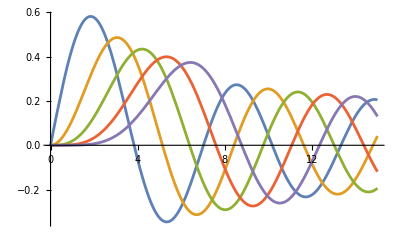

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,5}]],{x,0,15}]
```

```mathematica
MatrixForm/@JordanDecomposition[{{29,1,-21},{3,15,-3},{4,4,4}}]
```

{(1 | 3 | 4
0 | 3 | 1
1 | 2 | 1),(8 | 0 | 0
0 | 16 | 0
0 | 0 | 24)}

```mathematica
N[8*∑_(n=0)^1000 1/((4 n+2)^2-1)]
```

3.14109